```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
nomicartelle=Import["/Users/pagani/mg5_3.5/lista_cartellemumumassive.dat","List"]
quantities={aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}
```

{aatottformuu,altottl,mupemtomupemtt,mupemtomupemtt_v0,mupemtomupemtt_v2,nocut_mupemtomupemtt,nocuts_altottl,onlyphoton_altottl,onlyphoton_mupemtomupemtt,onlyphoton_mupemtomupemtt_v0,onlyphoton_mupemtomupemtt_v2,onlyphoton_nocut_mupemtomupemtt,onlyphoton_nocuts_altottl}

{aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}

```mathematica
namerun="distr2ndtry";
ptcutscale="0";
```

```mathematica
listaistogrammi=Table[0,{i,1,Length[nomicartelle]}];
Do[
nomi=.;
nhistos=.;
inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf";

If[i===6 || i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];


Estrai[inputname,quantities[[i]],nomi,nhistos],
{i,1,Length[nomicartelle]}]
```

```mathematica
unisci[x_]:=joinbin[x,1]
```

```mathematica
summed=sum[mumu[11],sum[aa[11],mua[11]]];
summedWWa=sum[mumu[11],sum[aaWW[11],muaWW[11]]];
```

ListLogPlot::ioproc: {{-5.,Indeterminate},{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{15.,Indeterminate},{20.,Indeterminate},{25.,Indeterminate},{30.,Indeterminate},{35.,Indeterminate},{40.,Indeterminate},«992»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListLogPlot::ioproc will be suppressed during this calculation.

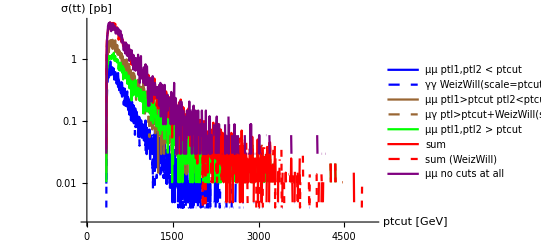

```mathematica
ListLogPlot[{unisci[aa[11]],unisci[aaWW[11]],unisci[mua[11]],unisci[ muaWW[11]],unisci[mumu[11]],unisci[summed],unisci[summedWWa],unisci[total[11]]},Joined->True,InterpolationOrder->10,AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple}]
```

```mathematica
nomi=.;
nhistos=.;
histos=.;
Estrai[inputname,histos,nomi,nhistos]
```

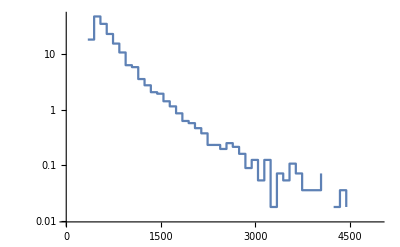

```mathematica
ListLogPlot[joinbin[histos[11],20],InterpolationOrder->0,Joined->True]
```

```mathematica
nomi
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_M},{14_DELTAR},{15_DELTAR},{16_DELTAR}}

```mathematica
Import[inputname]
```

<SAFheader>
</SAFheader>

<Histo>
  <Description>
    "1_THT"
    # nbins   xmin           xmax           
      40      0.000000e+00   5.000000e+02   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      0.000000e+00   0.000000e+00    # sum value*weight
      0.000000e+00   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      1.788105e+02   0.000000e+00    # bin 1 / 40
      0.000000e+00   0.000000e+00    # bin 2 / 40
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00    # bin 39 / 40
      0.000000e+00   0.000000e+00    # bin 40 / 40
      0.000000e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "2_MET"
    # nbins   xmin           xmax           
      40      0.000000e+00   5.000000e+02   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      5.513359e-07   0.000000e+00    # sum value*weight
      4.354902e-15   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      1.788105e+02   0.000000e+00    # bin 1 / 40
      0.000000e+00   0.000000e+00    # bin 2 / 40
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00    # bin 39 / 40
      0.000000e+00   0.000000e+00    # bin 40 / 40
      0.000000e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "3_SQRTS"
    # nbins   xmin           xmax           
      40      0.000000e+00   5.000000e+02   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      4.915407e+05   0.000000e+00    # sum value*weight
      2.091893e+09   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 40
      0.000000e+00   0.000000e+00    # bin 2 / 40
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      4.649072e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      3.933830e-01   0.000000e+00   
      5.006693e-01   0.000000e+00   
      4.112640e-01   0.000000e+00    # bin 39 / 40
      7.152418e-01   0.000000e+00    # bin 40 / 40
      1.752164e+02   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "4_PT"
    # nbins   xmin           xmax           
      40      0.000000e+00   5.000000e+02   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      3.336250e+04   0.000000e+00    # sum value*weight
      1.080815e+07   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      1.037101e+00   0.000000e+00    # bin 1 / 40
      3.415280e+00   0.000000e+00    # bin 2 / 40
      5.113979e+00   0.000000e+00   
      6.759035e+00   0.000000e+00   
      7.796136e+00   0.000000e+00   
      8.314686e+00   0.000000e+00   
      9.816694e+00   0.000000e+00   
      9.816694e+00   0.000000e+00   
      1.067498e+01   0.000000e+00   
      9.673645e+00   0.000000e+00   
      9.548478e+00   0.000000e+00   
      9.101452e+00   0.000000e+00   
      8.582902e+00   0.000000e+00   
      7.867660e+00   0.000000e+00   
      7.098775e+00   0.000000e+00   
      5.954388e+00   0.000000e+00   
      5.310670e+00   0.000000e+00   
      5.346432e+00   0.000000e+00   
      4.953049e+00   0.000000e+00   
      3.737138e+00   0.000000e+00   
      3.701376e+00   0.000000e+00   
      3.129183e+00   0.000000e+00   
      3.147064e+00   0.000000e+00   
      2.610633e+00   0.000000e+00   
      2.521227e+00   0.000000e+00   
      2.074201e+00   0.000000e+00   
      1.823867e+00   0.000000e+00   
      1.394722e+00   0.000000e+00   
      1.716580e+00   0.000000e+00   
      1.448365e+00   0.000000e+00   
      1.090744e+00   0.000000e+00   
      1.001339e+00   0.000000e+00   
      9.476954e-01   0.000000e+00   
      8.761712e-01   0.000000e+00   
      7.510039e-01   0.000000e+00   
      8.940523e-01   0.000000e+00   
      7.510039e-01   0.000000e+00   
      5.721934e-01   0.000000e+00   
      6.258366e-01   0.000000e+00    # bin 39 / 40
      3.755019e-01   0.000000e+00    # bin 40 / 40
      7.438515e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "5_ETA"
    # nbins   xmin           xmax           
      40      -1.000000e+01  1.000000e+01   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      8.705551e+01   0.000000e+00    # sum value*weight
      8.693059e+02   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 40
      0.000000e+00   0.000000e+00    # bin 2 / 40
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      5.543124e-01   0.000000e+00   
      1.251673e+00   0.000000e+00   
      2.968253e+00   0.000000e+00   
      4.720596e+00   0.000000e+00   
      6.794797e+00   0.000000e+00   
      9.369668e+00   0.000000e+00   
      1.164056e+01   0.000000e+00   
      1.210547e+01   0.000000e+00   
      1.194454e+01   0.000000e+00   
      1.140811e+01   0.000000e+00   
      1.269554e+01   0.000000e+00   
      1.387569e+01   0.000000e+00   
      1.450153e+01   0.000000e+00   
      1.557439e+01   0.000000e+00   
      1.401874e+01   0.000000e+00   
      1.269554e+01   0.000000e+00   
      9.441192e+00   0.000000e+00   
      6.633868e+00   0.000000e+00   
      3.307993e+00   0.000000e+00   
      1.752342e+00   0.000000e+00   
      6.794797e-01   0.000000e+00   
      4.291451e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00    # bin 39 / 40
      0.000000e+00   0.000000e+00    # bin 40 / 40
      0.000000e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "6_PT"
    # nbins   xmin           xmax           
      40      0.000000e+00   5.000000e+02   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      3.315531e+04   0.000000e+00    # sum value*weight
      1.036477e+07   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      8.582902e-01   0.000000e+00    # bin 1 / 40
      3.164945e+00   0.000000e+00    # bin 2 / 40
      5.328551e+00   0.000000e+00   
      6.848440e+00   0.000000e+00   
      7.992827e+00   0.000000e+00   
      8.672307e+00   0.000000e+00   
      9.190857e+00   0.000000e+00   
      1.063922e+01   0.000000e+00   
      9.941861e+00   0.000000e+00   
      1.001339e+01   0.000000e+00   
      9.566359e+00   0.000000e+00   
      8.940523e+00   0.000000e+00   
      8.529259e+00   0.000000e+00   
      7.849779e+00   0.000000e+00   
      7.223942e+00   0.000000e+00   
      5.864983e+00   0.000000e+00   
      5.668291e+00   0.000000e+00   
      5.131860e+00   0.000000e+00   
      4.845763e+00   0.000000e+00   
      3.844425e+00   0.000000e+00   
      3.665614e+00   0.000000e+00   
      2.932491e+00   0.000000e+00   
      2.717919e+00   0.000000e+00   
      2.467584e+00   0.000000e+00   
      2.753681e+00   0.000000e+00   
      2.235131e+00   0.000000e+00   
      1.788105e+00   0.000000e+00   
      1.591413e+00   0.000000e+00   
      1.591413e+00   0.000000e+00   
      1.502008e+00   0.000000e+00   
      1.358959e+00   0.000000e+00   
      1.108625e+00   0.000000e+00   
      1.054982e+00   0.000000e+00   
      8.940523e-01   0.000000e+00   
      8.761712e-01   0.000000e+00   
      8.225281e-01   0.000000e+00   
      8.404091e-01   0.000000e+00   
      7.152418e-01   0.000000e+00   
      4.470261e-01   0.000000e+00    # bin 39 / 40
      4.827882e-01   0.000000e+00    # bin 40 / 40
      6.848440e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "7_ETA"
    # nbins   xmin           xmax           
      40      -1.000000e+01  1.000000e+01   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      8.594632e+01   0.000000e+00    # sum value*weight
      8.459204e+02   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 40
      0.000000e+00   0.000000e+00    # bin 2 / 40
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      2.860967e-01   0.000000e+00   
      5.185503e-01   0.000000e+00   
      1.198030e+00   0.000000e+00   
      2.288774e+00   0.000000e+00   
      4.649072e+00   0.000000e+00   
      6.830559e+00   0.000000e+00   
      9.280262e+00   0.000000e+00   
      1.155116e+01   0.000000e+00   
      1.298164e+01   0.000000e+00   
      1.244521e+01   0.000000e+00   
      1.224852e+01   0.000000e+00   
      1.128294e+01   0.000000e+00   
      1.342866e+01   0.000000e+00   
      1.478762e+01   0.000000e+00   
      1.573532e+01   0.000000e+00   
      1.519889e+01   0.000000e+00   
      1.239156e+01   0.000000e+00   
      9.047809e+00   0.000000e+00   
      6.687511e+00   0.000000e+00   
      3.415280e+00   0.000000e+00   
      1.698699e+00   0.000000e+00   
      5.006693e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00    # bin 39 / 40
      0.000000e+00   0.000000e+00    # bin 40 / 40
      0.000000e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "8_PT"
    # nbins   xmin           xmax           
      40      0.000000e+00   5.000000e+02   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      5060           0               # nevents
      9.047809e+01   0.000000e+00    # sum of event-weights over events
      5060           0               # nentries
      9.047809e+01   0.000000e+00    # sum of event-weights over entries
      1.617843e+00   0.000000e+00    # sum weights^2
      3.919023e+03   0.000000e+00    # sum value*weight
      1.531919e+06   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      6.117106e+01   0.000000e+00    # bin 1 / 40
      6.437176e+00   0.000000e+00    # bin 2 / 40
      3.755019e+00   0.000000e+00   
      2.556989e+00   0.000000e+00   
      1.788105e+00   0.000000e+00   
      1.555651e+00   0.000000e+00   
      1.251673e+00   0.000000e+00   
      9.655764e-01   0.000000e+00   
      1.037101e+00   0.000000e+00   
      8.046470e-01   0.000000e+00   
      8.940523e-01   0.000000e+00   
      6.973608e-01   0.000000e+00   
      4.827882e-01   0.000000e+00   
      4.827882e-01   0.000000e+00   
      6.973608e-01   0.000000e+00   
      5.006693e-01   0.000000e+00   
      5.364314e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00    # bin 39 / 40
      1.072863e-01   0.000000e+00    # bin 40 / 40
      1.233792e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "9_ETA"
    # nbins   xmin           xmax           
      40      -1.000000e+01  1.000000e+01   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      5060           0               # nevents
      9.047809e+01   0.000000e+00    # sum of event-weights over events
      5060           0               # nentries
      9.047809e+01   0.000000e+00    # sum of event-weights over entries
      1.617843e+00   0.000000e+00    # sum weights^2
      7.017985e+02   0.000000e+00    # sum value*weight
      6.648941e+03   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      1.788105e-02   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 40
      1.788105e-02   0.000000e+00    # bin 2 / 40
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      3.755019e-01   0.000000e+00   
      6.794797e-01   0.000000e+00   
      1.698699e+00   0.000000e+00   
      2.378179e+00   0.000000e+00   
      3.701376e+00   0.000000e+00   
      4.130521e+00   0.000000e+00   
      3.951711e+00   0.000000e+00   
      4.345094e+00   0.000000e+00   
      4.112640e+00   0.000000e+00   
      4.291451e+00   0.000000e+00   
      4.756358e+00   0.000000e+00   
      4.559667e+00   0.000000e+00   
      4.434499e+00   0.000000e+00   
      4.345094e+00   0.000000e+00   
      4.345094e+00   0.000000e+00   
      4.702715e+00   0.000000e+00    # bin 39 / 40
      4.309332e+00   0.000000e+00    # bin 40 / 40
      2.621361e+01   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "10_M"
    # nbins   xmin           xmax           
      1000    0.000000e+00   5.000000e+03   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      5060           0               # nevents
      9.047809e+01   0.000000e+00    # sum of event-weights over events
      5060           0               # nentries
      9.047809e+01   0.000000e+00    # sum of event-weights over entries
      1.617843e+00   0.000000e+00    # sum weights^2
      1.588371e+05   0.000000e+00    # sum value*weight
      5.064610e+08   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 1000
      0.000000e+00   0.000000e+00    # bin 2 / 1000
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      3.755019e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.755019e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.933830e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.755019e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      2.145725e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      2.503346e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.072863e-01   0.000000e+00   
      0.000000e+00   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00    # bin 999 / 1000
      0.000000e+00   0.000000e+00    # bin 1000 / 1000
      5.185503e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "11_M"
    # nbins   xmin           xmax           
      1000    0.000000e+00   5.000000e+03   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      1.235027e+05   0.000000e+00    # sum value*weight
      1.181269e+08   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 1000
      0.000000e+00   0.000000e+00    # bin 2 / 1000
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-01   0.000000e+00   
      1.287435e+00   0.000000e+00   
      1.412603e+00   0.000000e+00   
      1.895391e+00   0.000000e+00   
      1.734461e+00   0.000000e+00   
      1.949034e+00   0.000000e+00   
      2.449703e+00   0.000000e+00   
      2.092082e+00   0.000000e+00   
      2.163606e+00   0.000000e+00   
      2.145725e+00   0.000000e+00   
      2.610633e+00   0.000000e+00   
      2.342417e+00   0.000000e+00   
      2.628514e+00   0.000000e+00   
      2.288774e+00   0.000000e+00   
      2.413941e+00   0.000000e+00   
      2.396060e+00   0.000000e+00   
      2.914610e+00   0.000000e+00   
      2.145725e+00   0.000000e+00   
      2.413941e+00   0.000000e+00   
      2.574870e+00   0.000000e+00   
      2.306655e+00   0.000000e+00   
      2.163606e+00   0.000000e+00   
      2.056320e+00   0.000000e+00   
      2.127844e+00   0.000000e+00   
      2.485465e+00   0.000000e+00   
      2.020558e+00   0.000000e+00   
      1.895391e+00   0.000000e+00   
      2.968253e+00   0.000000e+00   
      2.163606e+00   0.000000e+00   
      2.145725e+00   0.000000e+00   
      1.627175e+00   0.000000e+00   
      1.859629e+00   0.000000e+00   
      1.877510e+00   0.000000e+00   
      2.092082e+00   0.000000e+00   
      1.770223e+00   0.000000e+00   
      1.770223e+00   0.000000e+00   
      1.966915e+00   0.000000e+00   
      1.716580e+00   0.000000e+00   
      1.859629e+00   0.000000e+00   
      1.823867e+00   0.000000e+00   
      1.931153e+00   0.000000e+00   
      1.609294e+00   0.000000e+00   
      1.555651e+00   0.000000e+00   
      1.645056e+00   0.000000e+00   
      1.734461e+00   0.000000e+00   
      1.805986e+00   0.000000e+00   
      1.341078e+00   0.000000e+00   
      1.841748e+00   0.000000e+00   
      1.448365e+00   0.000000e+00   
      1.376840e+00   0.000000e+00   
      1.072863e+00   0.000000e+00   
      1.198030e+00   0.000000e+00   
      1.466246e+00   0.000000e+00   
      1.233792e+00   0.000000e+00   
      1.323197e+00   0.000000e+00   
      1.126506e+00   0.000000e+00   
      1.180149e+00   0.000000e+00   
      1.233792e+00   0.000000e+00   
      1.215911e+00   0.000000e+00   
      1.090744e+00   0.000000e+00   
      1.108625e+00   0.000000e+00   
      1.144387e+00   0.000000e+00   
      9.655764e-01   0.000000e+00   
      1.001339e+00   0.000000e+00   
      1.233792e+00   0.000000e+00   
      1.001339e+00   0.000000e+00   
      1.019220e+00   0.000000e+00   
      1.251673e+00   0.000000e+00   
      9.655764e-01   0.000000e+00   
      9.834575e-01   0.000000e+00   
      1.126506e+00   0.000000e+00   
      8.404091e-01   0.000000e+00   
      9.655764e-01   0.000000e+00   
      7.867660e-01   0.000000e+00   
      5.006693e-01   0.000000e+00   
      1.090744e+00   0.000000e+00   
      1.019220e+00   0.000000e+00   
      8.225281e-01   0.000000e+00   
      6.437176e-01   0.000000e+00   
      6.973608e-01   0.000000e+00   
      6.794797e-01   0.000000e+00   
      8.046470e-01   0.000000e+00   
      6.794797e-01   0.000000e+00   
      6.973608e-01   0.000000e+00   
      8.404091e-01   0.000000e+00   
      7.867660e-01   0.000000e+00   
      5.900745e-01   0.000000e+00   
      4.291451e-01   0.000000e+00   
      7.331228e-01   0.000000e+00   
      6.079555e-01   0.000000e+00   
      5.721934e-01   0.000000e+00   
      6.973608e-01   0.000000e+00   
      5.185503e-01   0.000000e+00   
      5.543124e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      6.615987e-01   0.000000e+00   
      5.006693e-01   0.000000e+00   
      6.079555e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      4.827882e-01   0.000000e+00   
      7.331228e-01   0.000000e+00   
      4.649072e-01   0.000000e+00   
      4.470261e-01   0.000000e+00   
      5.543124e-01   0.000000e+00   
      5.185503e-01   0.000000e+00   
      4.827882e-01   0.000000e+00   
      6.258366e-01   0.000000e+00   
      5.185503e-01   0.000000e+00   
      5.543124e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      4.470261e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      4.291451e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      4.470261e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      3.933830e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.933830e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      3.933830e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00    # bin 999 / 1000
      0.000000e+00   0.000000e+00    # bin 1000 / 1000
      8.940523e-02   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "12_M"
    # nbins   xmin           xmax           
      1000    0.000000e+00   5.000000e+03   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      5060           0               # nevents
      9.047809e+01   0.000000e+00    # sum of event-weights over events
      5060           0               # nentries
      9.047809e+01   0.000000e+00    # sum of event-weights over entries
      1.617843e+00   0.000000e+00    # sum weights^2
      2.495912e+05   0.000000e+00    # sum value*weight
      1.062723e+09   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 1000
      0.000000e+00   0.000000e+00    # bin 2 / 1000
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00    # bin 999 / 1000
      8.940523e-02   0.000000e+00    # bin 1000 / 1000
      1.294588e+01   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "13_M"
    # nbins   xmin           xmax           
      1000    0.000000e+00   5.000000e+03   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      5060           0               # nevents
      9.047809e+01   0.000000e+00    # sum of event-weights over events
      5060           0               # nentries
      9.047809e+01   0.000000e+00    # sum of event-weights over entries
      1.617843e+00   0.000000e+00    # sum weights^2
      1.595930e+05   0.000000e+00    # sum value*weight
      5.005677e+08   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      0.000000e+00   0.000000e+00    # bin 1 / 1000
      0.000000e+00   0.000000e+00    # bin 2 / 1000
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.933830e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.933830e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.755019e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.860967e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      2.324536e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      2.682157e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      2.503346e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      2.503346e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      2.145725e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.430484e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.251673e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.609294e-01   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      7.152418e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      3.576209e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      3.576209e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      5.364314e-02   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00    # bin 999 / 1000
      5.364314e-02   0.000000e+00    # bin 1000 / 1000
      4.506023e+00   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "14_DELTAR"
    # nbins   xmin           xmax           
      40      0.000000e+00   1.000000e+01   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      5060           0               # nevents
      9.047809e+01   0.000000e+00    # sum of event-weights over events
      5060           0               # nentries
      9.047809e+01   0.000000e+00    # sum of event-weights over entries
      1.617843e+00   0.000000e+00    # sum weights^2
      7.261482e+02   0.000000e+00    # sum value*weight
      7.131385e+03   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      8.940523e-02   0.000000e+00    # bin 1 / 40
      1.251673e-01   0.000000e+00    # bin 2 / 40
      1.430484e-01   0.000000e+00   
      2.682157e-01   0.000000e+00   
      1.788105e-01   0.000000e+00   
      3.397399e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      6.973608e-01   0.000000e+00   
      1.001339e+00   0.000000e+00   
      8.225281e-01   0.000000e+00   
      1.180149e+00   0.000000e+00   
      1.573532e+00   0.000000e+00   
      2.109963e+00   0.000000e+00   
      1.859629e+00   0.000000e+00   
      1.537770e+00   0.000000e+00   
      2.056320e+00   0.000000e+00   
      2.074201e+00   0.000000e+00   
      1.841748e+00   0.000000e+00   
      2.288774e+00   0.000000e+00   
      1.805986e+00   0.000000e+00   
      2.127844e+00   0.000000e+00   
      2.235131e+00   0.000000e+00   
      2.199369e+00   0.000000e+00   
      2.109963e+00   0.000000e+00   
      2.074201e+00   0.000000e+00   
      2.306655e+00   0.000000e+00   
      1.823867e+00   0.000000e+00   
      1.877510e+00   0.000000e+00   
      2.467584e+00   0.000000e+00   
      2.342417e+00   0.000000e+00   
      2.360298e+00   0.000000e+00   
      2.235131e+00   0.000000e+00   
      2.038439e+00   0.000000e+00   
      1.949034e+00   0.000000e+00   
      2.253012e+00   0.000000e+00   
      1.770223e+00   0.000000e+00   
      1.931153e+00   0.000000e+00   
      1.805986e+00   0.000000e+00   
      1.913272e+00   0.000000e+00    # bin 39 / 40
      1.752342e+00   0.000000e+00    # bin 40 / 40
      2.660700e+01   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "15_DELTAR"
    # nbins   xmin           xmax           
      40      0.000000e+00   1.000000e+01   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      10000          0               # nevents
      1.788105e+02   0.000000e+00    # sum of event-weights over events
      10000          0               # nentries
      1.788105e+02   0.000000e+00    # sum of event-weights over entries
      3.197318e+00   0.000000e+00    # sum weights^2
      6.204652e+02   0.000000e+00    # sum value*weight
      2.268566e+03   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      1.251673e-01   0.000000e+00    # bin 1 / 40
      1.609294e-01   0.000000e+00    # bin 2 / 40
      2.860967e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      7.688849e-01   0.000000e+00   
      6.973608e-01   0.000000e+00   
      8.761712e-01   0.000000e+00   
      1.269554e+00   0.000000e+00   
      1.323197e+00   0.000000e+00   
      2.181488e+00   0.000000e+00   
      3.844425e+00   0.000000e+00   
      7.992827e+00   0.000000e+00   
      6.340619e+01   0.000000e+00   
      3.687072e+01   0.000000e+00   
      1.886450e+01   0.000000e+00   
      1.178361e+01   0.000000e+00   
      7.867660e+00   0.000000e+00   
      5.042455e+00   0.000000e+00   
      3.772901e+00   0.000000e+00   
      2.789443e+00   0.000000e+00   
      2.199369e+00   0.000000e+00   
      1.537770e+00   0.000000e+00   
      1.233792e+00   0.000000e+00   
      8.582902e-01   0.000000e+00   
      6.079555e-01   0.000000e+00   
      4.112640e-01   0.000000e+00   
      4.649072e-01   0.000000e+00   
      3.039778e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.072863e-01   0.000000e+00   
      8.940523e-02   0.000000e+00   
      1.072863e-01   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      7.152418e-02   0.000000e+00   
      0.000000e+00   0.000000e+00   
      1.788105e-02   0.000000e+00   
      5.364314e-02   0.000000e+00   
      3.576209e-02   0.000000e+00    # bin 39 / 40
      0.000000e+00   0.000000e+00    # bin 40 / 40
      3.576209e-02   0.000000e+00    # overflow
  </Data>
</Histo>

<Histo>
  <Description>
    "16_DELTAR"
    # nbins   xmin           xmax           
      40      0.000000e+00   1.000000e+01   
    # Defined regions
      myregion    # Region nr. 1
  </Description>
  <Statistics>
      5060           0               # nevents
      9.047809e+01   0.000000e+00    # sum of event-weights over events
      5060           0               # nentries
      9.047809e+01   0.000000e+00    # sum of event-weights over entries
      1.617843e+00   0.000000e+00    # sum weights^2
      7.302034e+02   0.000000e+00    # sum value*weight
      7.183670e+03   0.000000e+00    # sum value^2*weight
  </Statistics>
  <Data>
      0.000000e+00   0.000000e+00    # underflow
      1.788105e-02   0.000000e+00    # bin 1 / 40
      5.364314e-02   0.000000e+00    # bin 2 / 40
      1.072863e-01   0.000000e+00   
      1.966915e-01   0.000000e+00   
      1.609294e-01   0.000000e+00   
      3.218588e-01   0.000000e+00   
      3.576209e-01   0.000000e+00   
      3.755019e-01   0.000000e+00   
      7.510039e-01   0.000000e+00   
      9.834575e-01   0.000000e+00   
      1.573532e+00   0.000000e+00   
      1.555651e+00   0.000000e+00   
      2.253012e+00   0.000000e+00   
      1.841748e+00   0.000000e+00   
      1.949034e+00   0.000000e+00   
      1.645056e+00   0.000000e+00   
      1.859629e+00   0.000000e+00   
      1.805986e+00   0.000000e+00   
      1.931153e+00   0.000000e+00   
      2.074201e+00   0.000000e+00   
      1.931153e+00   0.000000e+00   
      2.109963e+00   0.000000e+00   
      2.396060e+00   0.000000e+00   
      2.217250e+00   0.000000e+00   
      2.378179e+00   0.000000e+00   
      1.966915e+00   0.000000e+00   
      2.306655e+00   0.000000e+00   
      2.181488e+00   0.000000e+00   
      2.127844e+00   0.000000e+00   
      2.092082e+00   0.000000e+00   
      2.467584e+00   0.000000e+00   
      1.698699e+00   0.000000e+00   
      2.431822e+00   0.000000e+00   
      1.913272e+00   0.000000e+00   
      2.163606e+00   0.000000e+00   
      2.074201e+00   0.000000e+00   
      1.805986e+00   0.000000e+00   
      1.877510e+00   0.000000e+00   
      1.877510e+00   0.000000e+00    # bin 39 / 40
      1.698699e+00   0.000000e+00    # bin 40 / 40
      2.694673e+01   0.000000e+00    # overflow
  </Data>
</Histo>

<SAFfooter>
</SAFfooter>